Set up constants for Sack-Biedenharn-Breit potential:

```mathematica
m=938.272046(*Mega ElectronVolt*);
mred=4/5*m(*Reduced Mass*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
V=-47.32 (*Mega ElectronVolt*);
η=0.189034(*Femto Meter^-2*);
VLS=5.8554/η(*Mega ElectronVolt*Femto Meter^2*);
V0[r_]:=V*Exp[-η*r^2];
V1[k_,b_,r_]:=k*b*VLS*(-2*E^(-η*r^2)*η);
```

Set up Glauber phases for spin-orbit scattering following Glauber and Gottfried (chapter 8, problem 11).

```mathematica
Δ0[k_,b_]:=-2*mred/(k*(ℏc)^2)*NIntegrate[V0[r]*r/Sqrt[r^2-b^2],{r,b,Infinity}]
Δ1[k_,b_]:=-2*mred/(k*(ℏc)^2)*NIntegrate[V1[k,b,r]*r/Sqrt[r^2-b^2],{r,b,Infinity}]
g[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*(Exp[2*I*Δ0[k,b]]*Cos[2*k*b*Δ1[k,b]]-1),{b,0,Infinity}]
h[k_,θ_]:=I*k*NIntegrate[b*BesselJ[1,2*k*b*Sin[θ/2]]*Exp[2*I*Δ0[k,b]]*Sin[2*k*b*Δ1[k,b]],{b,0,Infinity}]
```

Use optical theorem to calculate total cross section for energies in same range as data from Schwaller. There is an extra factor of 10 in the calculation to convert from fm^2 to millibarns:

```mathematica
tabsbb=Table[{k,4*Pi*Im[g[k,0]]/k*10},{k,3,5.5,.1}]
```

{{3.,2041.53},{3.1,2022.64},{3.2,1987.83},{3.3,1943.39},{3.4,1897.01},{3.5,1856.62},{3.6,1829.34},{3.7,1820.48},{3.8,1832.81},{3.9,1866.24},{4.,1917.81},{4.1,1982.14},{4.2,2052.14},{4.3,2119.95},{4.4,2178.02},{4.5,2220.04},{4.6,2241.8},{4.7,2241.71},{4.8,2220.96},{4.9,2183.39},{5.,2134.93},{5.1,2082.86},{5.2,2034.83},{5.3,1997.9},{5.4,1977.63},{5.5,1977.38}}

```mathematica
interpsbb=Interpolation[tabsbb];
```

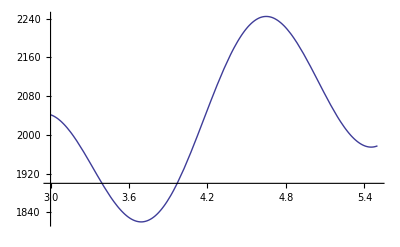

```mathematica
Plot[interpsbb[t],{t,3,5.5}]
```

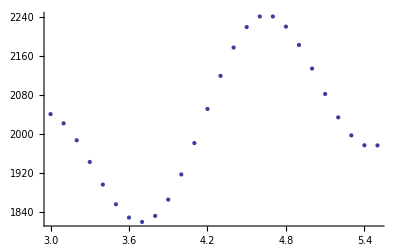

```mathematica
ListPlot[tabsbb]
```

Now set up constants for Satchler potential (also described in Kukulin):

```mathematica
m=938.272046(*Mega ElectronVolt*);
mred=4/5*m(*Reduced Mass*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
Rc=2.0(*Femto Meter*);
ac=0.70(*Femto Meter*);
Rso=1.5(*Femto Meter*);
aso=0.35(*Femto Meter*);
V=-43 (*Mega ElectronVolt*);
Vso=40.0(*Mega ElectronVolt*);
V0[r_]:=V/(1+Exp[(r-Rc)/ac]);
V1[k_,b_,r_]:=k*b*Vso/(-2 aso r-2 aso r Cosh[(r-Rso)/aso]);
```

Redefine Glauber phases in terms of new potential:

```mathematica
Δ0[k_,b_]:=-2*mred/(k*(ℏc)^2)*NIntegrate[V0[r]*r/Sqrt[r^2-b^2],{r,b,Infinity}]
Δ1[k_,b_]:=-2*mred/(k*(ℏc)^2)*NIntegrate[V1[k,b,r]*r/Sqrt[r^2-b^2],{r,b,Infinity}]
g[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*(Exp[2*I*Δ0[k,b]]*Cos[2*k*b*Δ1[k,b]]-1),{b,0,Infinity}]
h[k_,θ_]:=I*k*NIntegrate[b*BesselJ[1,2*k*b*Sin[θ/2]]*Exp[2*I*Δ0[k,b]]*Sin[2*k*b*Δ1[k,b]],{b,0,Infinity}]
```

Use optical theorem to get cross sections again:

```mathematica
4*Pi*Im[g[Sqrt[2*m*224]/ℏc,0]]/(Sqrt[2*m*232]/ℏc)*10
```

709.004

```mathematica
tabsat=Table[{k,4*Pi*Im[g[k,0]]/k*10},{k,3,5.5,.1}]
```

{{3.,709.891},{3.1,711.594},{3.2,715.543},{3.3,722.814},{3.4,733.341},{3.5,745.959},{3.6,758.74},{3.7,769.509},{3.8,776.418},{3.9,778.433},{4.,775.627},{4.1,769.202},{4.2,761.259},{4.3,754.347},{4.4,750.908},{4.5,752.734},{4.6,760.56},{4.7,773.872},{4.8,790.986},{4.9,809.367},{5.,826.135},{5.1,838.65},{5.2,845.055},{5.3,844.66},{5.4,838.104},{5.5,827.243}}

```mathematica
interpsat=Interpolation[tabsat];
```

Compare to data from Schwaller:

```mathematica
tabdat={{Sqrt[2*m*224]/ℏc,106.3},{Sqrt[2*m*273]/ℏc,105.7},{Sqrt[2*m*345]/ℏc,106.8},{Sqrt[2*m*413]/ℏc,110.8},{Sqrt[2*m*430]/ℏc,112.8},{Sqrt[2*m*491]/ℏc,117.6},{Sqrt[2*m*563]/ℏc,123.7}};
```

```mathematica
interpdat=Interpolation[tabdat];
```

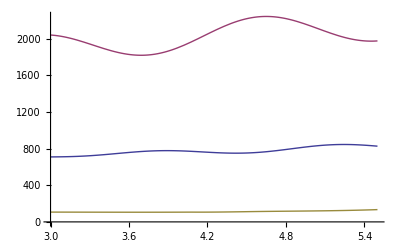

```mathematica
Plot[{interpsat[t],interpsbb[t],interpdat[t]},{t,3,5.5}]
```

Both methods seem to be quite overcompensating. I can calculate what the eikonal corrections are and see if they help , but these calculations are done at forward scattering at energies where the Glauber approximation should be valid, so I don't know how much good they will do.

```mathematica
Interp=Interpolation[{{30.35,70},{32.15,73},{34.25,82},{36.9,95},{39.75,105},{45,109}}]
```

InterpolatingFunction[{{30.35,45.}},<>]

```mathematica
Interp[52.3]
```

InterpolatingFunction::dmval: Input value {52.3`} lies outside the range of data in the interpolating function. Extrapolation will be used.

72.3194

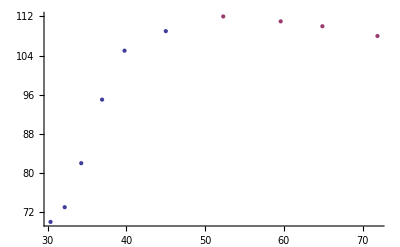

```mathematica
ListPlot[{{{30.35,70},{32.15,73},{34.25,82},{36.9,95},{39.75,105},{45,109}},{{52.3,112},{59.6,111},{64.9,110},{71.9,108}}}]
```